## Definitions

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/mu3q/Dropbox/Source/Mathematica/kinetics-toolbox

```mathematica
Run["git describe > version.txt"] ; FilePrint["version.txt"]
```

v1.0.0-beta

```mathematica
Print["Kinetics Toolbox v1.0.0-beta\n(c)2018-2020 Marcel Utz"]
```

Kinetics Toolbox v1.0.0-beta
(c)2018-2020 Marcel Utz

```mathematica
Format[Reaction[A_-> B_,k_]] := Infix[f[A,B],Labeled["⟶",k,{Top}]]
```

```mathematica
reac1= Reaction[ A + 2B ->  Q + F,k1] 
reac2=Reaction[2F  -> W+A,k2]
```

(A+2 B)⟶k1(F+Q)

(2 F)⟶k2(A+W)

```mathematica
transp1=Transport[Aa->Ab,q/Va,q/Vb]
```

Transport[Aa→Ab,q/Va,q/Vb]

```mathematica
Educts[  Reaction[Q_-> Y_,___] | Transport[Q_-> Y_,___]  ]  := Flatten[{Q  /. {Plus->List,A_Symbol|A_Subscript->Coeff[A,-1],Times[n_Integer,A_Symbol|A_Subscript]->Coeff[A,-n]} }] ;
Educts[ S_Source | S_Supply] := {} ;
```

```mathematica
Products[  Reaction[Q_-> Y_,___] |  Transport[Q_-> Y_,___]]  := Flatten[ { Y  /. {Plus->List,A_Symbol|A_Subscript->Coeff[A,1],Times[n_Integer,A_Symbol|A_Subscript]->Coeff[A,n]} } ] ;
 Products[ Source[A_Symbol | A_Subscript,___] ] := {Coeff[A,1]} ;
 Products[ Supply[A_Symbol | A_Subscript,___] ] := {Coeff[A,1]} ;
```

```mathematica
Educts[reac2]
```

{Coeff[F,-2]}

```mathematica
Products[transp1]
```

{Coeff[Ab,1]}

```mathematica
Educts[transp1]
```

{Coeff[Aa,-1]}

```mathematica
RateExpression[A_Reaction,S_,t_,___] := 
A[[2]] Product[ l[[1]][t] ^ (-l[[2]]),{l,Educts[A]}]
```

```mathematica
RateExpression[Transport[Q_->Y_,k1_,k2_],S_,t_] :=  If[S===Q, k1 Q[t], If[S===Y,k2 Q[t],0]]
```

```mathematica
RateExpression[Source[Y_Symbol|Y_Subscript,y0_,k_],S_,t_] := If[S===Y, k(y0-Y[t]),0]
```

```mathematica
RateExpression[Supply[Q_Symbol|Q_Subscript,k_],S_,t_] := If[S===Q,k,0]
```

```mathematica
RateExpression[Source[H,h0,k],H,x]
```

k (h0-H[x])

```mathematica
StoichiometricCoefficient[R_Reaction|R_Transport|R_Source|R_Supply, S_Symbol | S_Subscript] :=
  Module[{m=Join[Educts[R],Products[R]]},
Total[Cases[m,Coeff[S,k_]:> k] /. _Missing->0 ]]
```

```mathematica
StoichiometricCoefficient[transp1,X]
```

0

```mathematica
RateEquation[Reac_List, S_Symbol | S_Subscript, t_] := Module[{},
D[S[t],t]==Sum[ RateExpression[r,S,t] StoichiometricCoefficient[r,S],{r,Reac}]
]
```

```mathematica
RateEquation[{reac1,reac2,transp1},A,t]
```

A'[t]==-k1 A[t] B[t]^2+k2 F[t]^2

```mathematica
ReactionSpecies[R_Reaction | R_Transport | R_Source] :=  Join[Educts[R],Products[R]] /. Coeff[A_,_]->A ;
SetAttributes[ReactionSpecies,Listable]
```

Equilibrium reactions are evaluated to a pair of reactions:

```mathematica
EqReaction[A_ ->  B_ , k1_,k2_] := Sequence[
Reaction [A->B, k1], Reaction[B->A,k2]]
```

Transports can be generated simultaneously by threading over lists:

```mathematica
Transport[{A_},{B_},k1_,k2_] :=  Transport[A->B,k1,k2];
Transport[A_List,B_List,k1_,k2_] := 
 Sequence[Transport[First[A]->First[B],k1,k2], Transport[Rest[A],Rest[B],k1,k2]] ;
```

Sometimes it is convenient to indicate initial conditions only for a few species, with all others assumed to be zero. This can be automated using the following tool:

```mathematica
CompleteInitialConditions[vars_, conds_] := 
Module[ {m,  q=conds/. a_[_]==_ ->a },
v=Complement[vars,q];
Join[conds,Table[k[0]==0,{k,v}]]
]
```

Reactions can automatically be made specific to a particular region by adding indices to the symbols:

```mathematica
RegionIndices[vars_List,subs_Symbol] := Table[ s->Subscript[s,subs],{s,vars}]
```

We also need a way to generate transport objects for all species from region α to region β:

```mathematica
RegionTransports[vars_List,α_,β_,k1_,k2_] := 
Table[ Transport[ Subscript[s,α]-> Subscript[s,β],k1,k2],{s,vars}]
```

## Example 1: catalytic conversion of pH2 and oH2

We model the interconversion of pH2 and oH2 catalysed by R:

```mathematica
reacs={Reaction[R+pH2 -> pRH2, k1], 
Reaction[R+oH2->oRH2,k1],
Reaction[oRH2-> R + oH2,k1],
Reaction[pRH2 -> R+pH2,k1],
Reaction[pRH2 -> oRH2, k2],
Reaction[oRH2-> pRH2, k2/3]}
```

{(pH2+R)⟶k1pRH2,(oH2+R)⟶k1oRH2,oRH2⟶k1(oH2+R),pRH2⟶k1(pH2+R),pRH2⟶k2oRH2,oRH2⟶k2/3pRH2}

```mathematica
RateEquation[reacs,pH2,t]
```

pH2'[t]==k1 pRH2[t]-k1 pH2[t] R[t]

```mathematica
vars=Union@Flatten@ReactionSpecies[reacs]
```

{oH2,oRH2,pH2,pRH2,R}

All rate equations for the the specified reactions can be computed conveniently like this:

```mathematica
eqns=Table[ RateEquation[reacs,S,t],{S,vars}]
```

{oH2'[t]==k1 oRH2[t]-k1 oH2[t] R[t],oRH2'[t]==-k1 oRH2[t]-1/3 k2 oRH2[t]+k2 pRH2[t]+k1 oH2[t] R[t],pH2'[t]==k1 pRH2[t]-k1 pH2[t] R[t],pRH2'[t]==1/3 k2 oRH2[t]-k1 pRH2[t]-k2 pRH2[t]+k1 pH2[t] R[t],R'[t]==k1 oRH2[t]+k1 pRH2[t]-k1 oH2[t] R[t]-k1 pH2[t] R[t]}

```mathematica
initial={oH2[0]==0.5, oRH2[0]==0,pH2[0]==0.5,pRH2[0]==0,R[0]==0.1}
```

{oH2[0]==0.5,oRH2[0]==0,pH2[0]==0.5,pRH2[0]==0,R[0]==0.1}

```mathematica
sol=First@NDSolve[Join[eqns,initial]/.{k1->0.2,k2->10.0},vars,{t,0,1000}]
```

{oH2→InterpolatingFunction[…],oRH2→InterpolatingFunction[…],pH2→InterpolatingFunction[…],pRH2→InterpolatingFunction[…],R→InterpolatingFunction[…]}

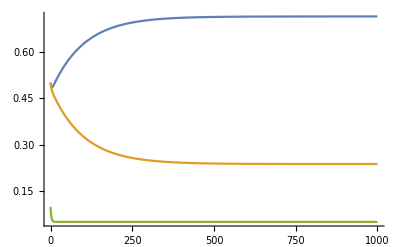

```mathematica
Plot[Evaluate[{oH2[t],pH2[t],R[t]} /. sol], {t,0,1000},PlotRange->All]
```

## Example 2: Equilibration of concentration between two vessels

```mathematica
reacs={Transport[A->B,q/Va,q/Vb],Transport[B->A,q/Vb,q/Va]}
```

{Transport[A→B,q/Va,q/Vb],Transport[B→A,q/Vb,q/Va]}

```mathematica
vars=Union@Flatten@ReactionSpecies[reacs]
```

{A,B}

```mathematica
eqns=Table[ RateEquation[reacs,S,t],{S,Union@Flatten@ReactionSpecies[reacs]}]
```

{A'[t]==-(q A[t])/Va+(q B[t])/Va,B'[t]==(q A[t])/Vb-(q B[t])/Vb}

```mathematica
initial={A[0]==1.,B[0]==0.}
```

{A[0]==1.,B[0]==0.}

```mathematica
sol=First@NDSolve[Join[eqns,initial]/.{q->0.05,Va->1,Vb->1},vars,{t,0,100}]
```

{A→InterpolatingFunction[…],B→InterpolatingFunction[…]}

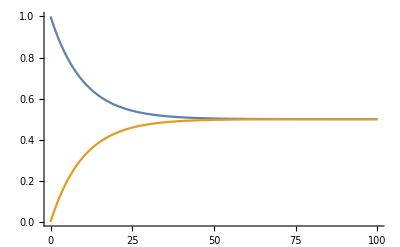

```mathematica
Plot[Evaluate[{A[t],B[t]} /. sol], {t,0,100},PlotRange->All]
```

In this case, the integration can be done analytically, as well:

```mathematica
sol=First@DSolve[Join[eqns,initial],vars,t]
```

{A→Function[{t},(1. (1. Va+1. ⅇ^((q t (-Va-Vb))/(Va Vb)) Vb))/(Va+Vb)],B→Function[{t},-(1. (-1.+ⅇ^((q t (-Va-Vb))/(Va Vb))) Va)/(Va+Vb)]}

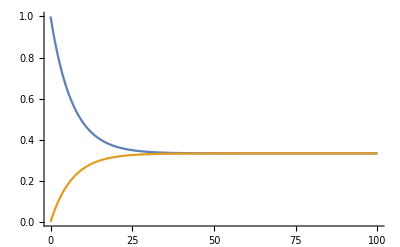

```mathematica
Plot[Evaluate[{A[t],B[t]} /. sol/.{q->0.1,Va->1,Vb->2}], {t,0,100},PlotRange->All]
```